## Comparison between Darlington pair heat flows and single transistor heat flows

```mathematica
Tint=0.02;
```

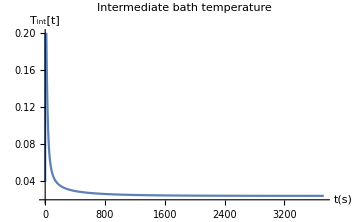
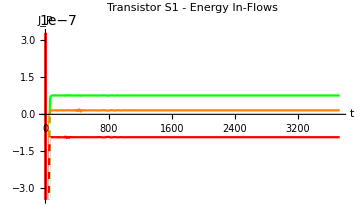
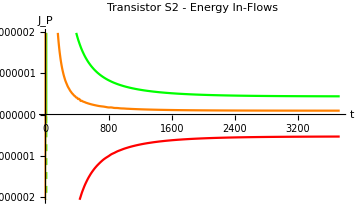
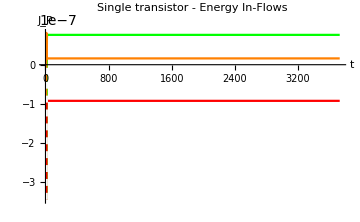

```mathematica
Tint=0.04;
```

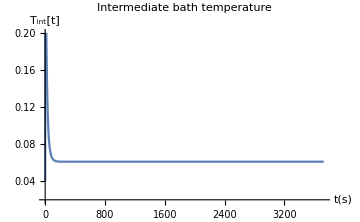
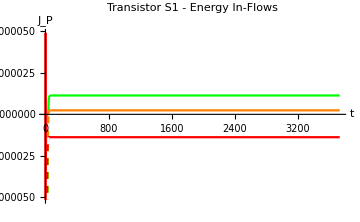
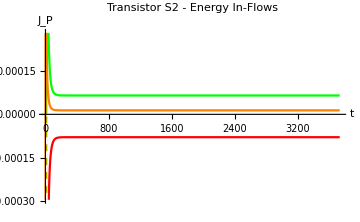
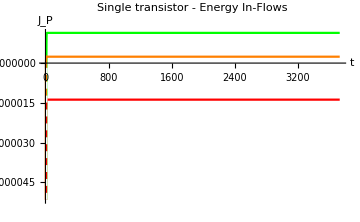

```mathematica
Tint=0.06;
```

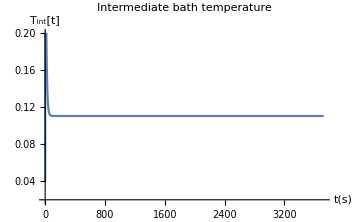
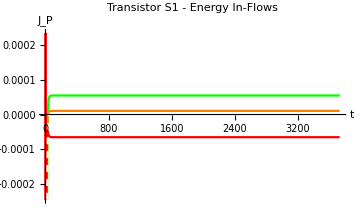
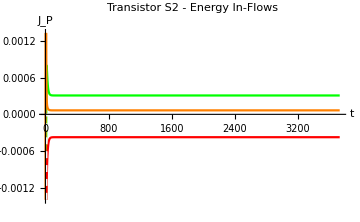
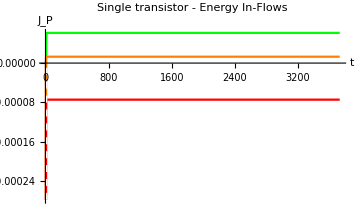

```mathematica
Tint=0.1;
```

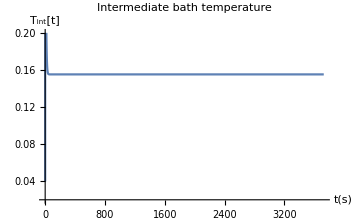
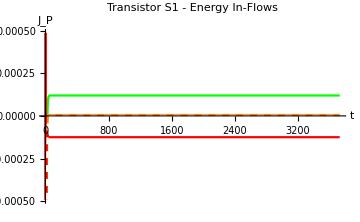
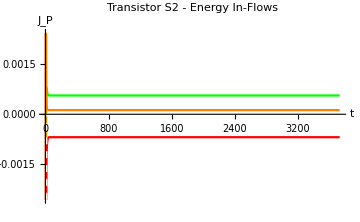
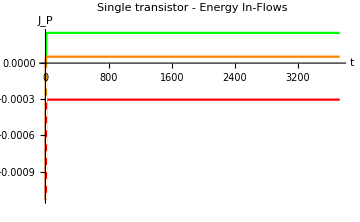

```mathematica
Tint=0.2;
```

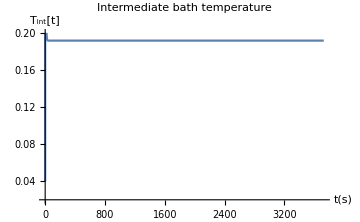
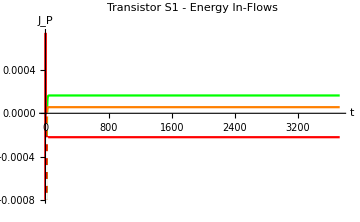
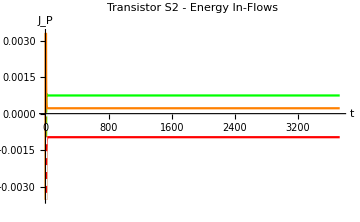
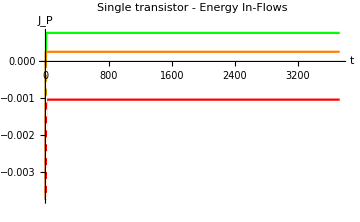

## Plots for adjusting T_CNT while keeping Ω constant (operation as a thermal transistor)

### For the single transistor case

Run the following two lines in the Optically Controlled Thermal Gate 2, after running it until the visualization section

```mathematica
PlotEngyFlowsWithTM[T1_,T2min_,T2max_,T3_,κ1_,κ2_,κ3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Ωs_,Tres_,legends_]:=Module[{tempx,tempy,temp},
tempx=Table[{T2,T2,T2,T2},{T2,T2min,T2max,Tres}];
tempy=Table[varEngyFunc[T1,T2,T3,κ1,κ2,κ3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωs,unitassum],{T2,T2min,T2max,Tres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,i]]}],{i,1,4}];
ListPlot[temp,PlotRange->{{T2min,T2max},{-0.001,0.001}},
	AxesLabel->{Style["T_M"],Style["J_P"]},Joined->True,
	PlotStyle->{{Green},{Orange},{Red},{Blue}},
	PlotLegends->legends &&{Style["J_L"],Style["J_M"],Style["J_R"],Style["J_F"]}]
]
```

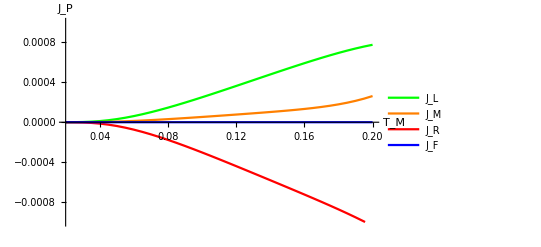

```mathematica
Module[{T1,T2min,T2max,κ1,κ2,κ3,T3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωs,Tres},
T1=0.2Tconv;T2min=0.02Tconv;T2max=0.20Tconv;T3=0.02Tconv;
κ1=1;κ2=1;κ3=1;
ωLs=0ωconv;ωMs=0ωconv;ωRs=0ωconv;
ωLMs=0.9ωconv;ωMRs=1.1ωconv;ωRLs=0ωconv;
Ωs=0.0ωconv;Tres=0.005Tconv;
PlotEngyFlowsWithTM[T1,T2min,T2max,T3,κ1,κ2,κ3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωs,Tres,True]
]
```

### For the Darlington pair case

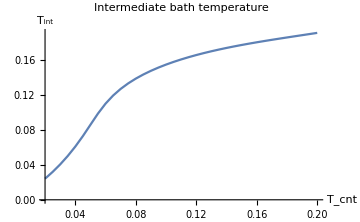
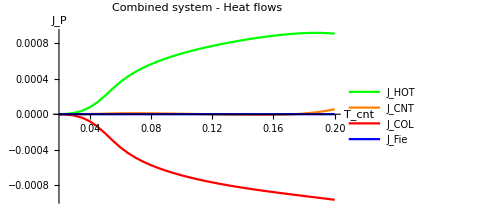
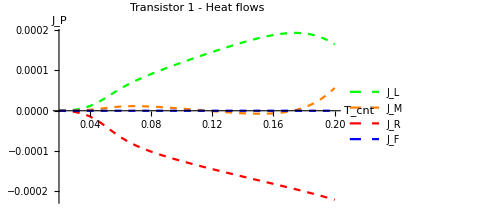
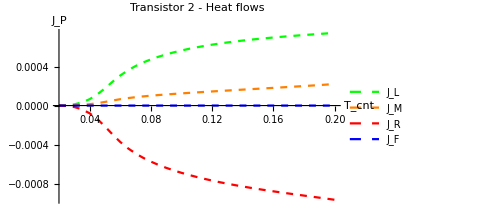

## Plots for adjusting Ω while keeping T_CNT constant (operation as an optically controlled thermal gate)

### For the single transistor case

Run the following two lines in the Optically Controlled Thermal Gate 2, after running it until the visualization section

```mathematica
PlotEngyFlowsWithΩ[T1_,T2_,T3_,κ1_,κ2_,κ3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Ωmin_,Ωmax_,Ωres_,plotrange_]:=Module[{tempx,tempy,temp},
tempy=Table[varEngyFunc[T1,T2,T3,κ1,κ2,κ3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ω,unitassum],{Ω,Ωmin,Ωmax,Ωres}];
tempx=Table[{Ω,Ω,Ω,Ω},{Ω,Ωmin,Ωmax,Ωres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,i]]}],{i,1,4}];
ListPlot[temp,AxesLabel->{Style["Ω"],Style["J_P"]},
	Joined->True,PlotStyle->{Green,Orange,Red,Blue},
	PlotLegends->{Style["J_L"],Style["J_M"],Style["J_R"],Style["J_F"]},
	PlotRange->plotrange]
]
```

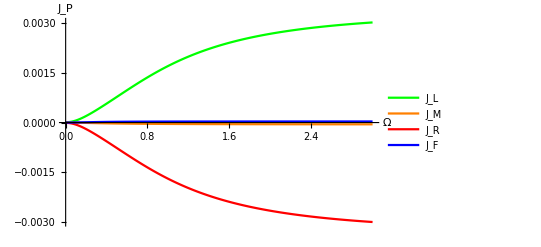

```mathematica
Module[{T1,T2,T3,κ1,κ2,κ3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωmin,Ωmax,Ωres},
T1=0.2Tconv;T2=0.02Tconv;T3=0.02Tconv;
κ1=1;κ2=1;κ3=1;
ωLs=0ωconv;ωMs=0.1ωconv;ωRs=0ωconv;
ωLMs=1ωconv;ωMRs=1ωconv;ωRLs=0ωconv;
Ωmin=0ωconv;Ωmax=3ωconv;Ωres=0.02ωconv;
PlotEngyFlowsWithΩ[T1,T2,T3,κ1,κ2,κ3,ωLs,ωMs,ωRs,ωLMs,ωMRs,ωRLs,Ωmin,Ωmax,Ωres,Full]
]
```

### For the Darlington pair case

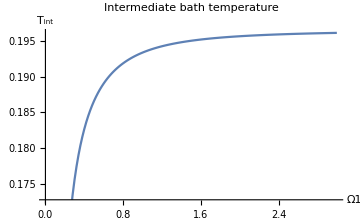
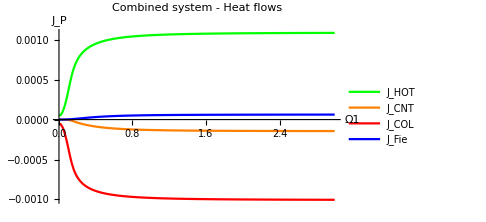
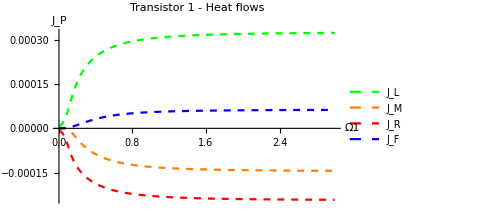
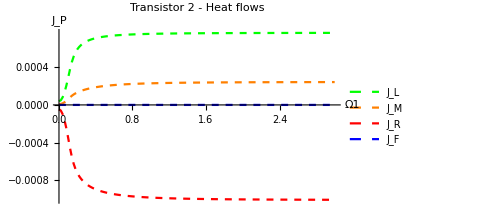

## Images for paper

## Plots for total thermal flow through B_INT

Under a temperature-controlled configuration

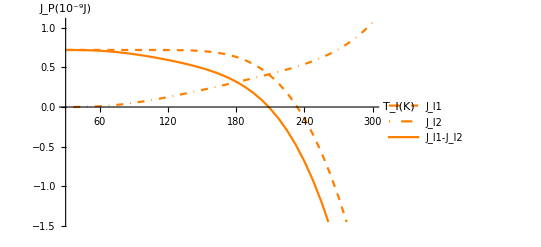

Under an optically-controlled configuration

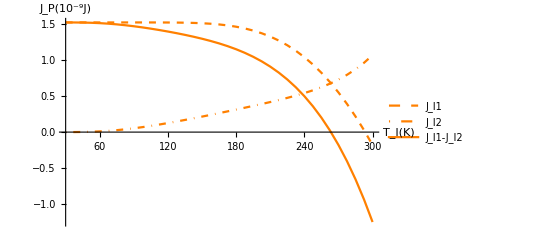

## Plots for adjusting T_CNT while keeping Ω constant (operation as a thermal transistor)

Temperature of the intermediate bath

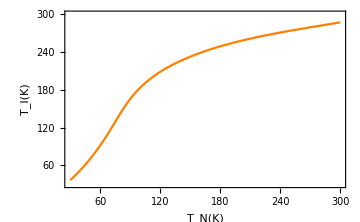

Heat flow comparison between Darlington pair and a single transistor

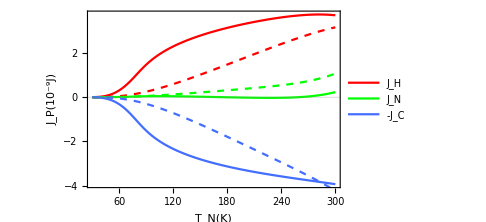
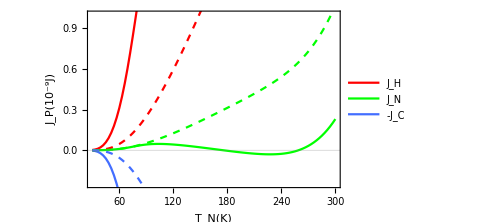

Heat flows of individual transistors

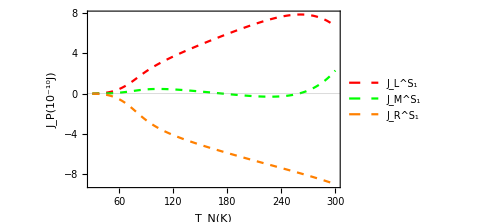
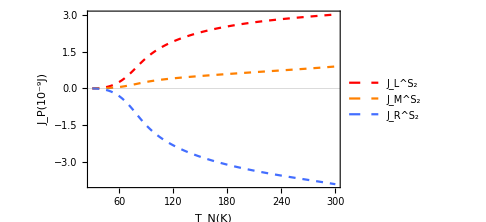

Absolute thermal efficiency

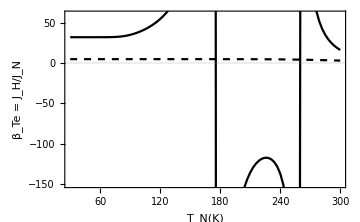

Delta thermal efficiency (amplification factor)

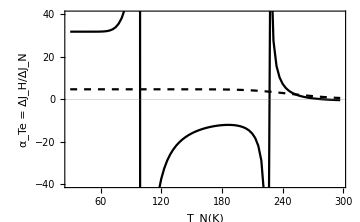

Sensitivity to the optical field

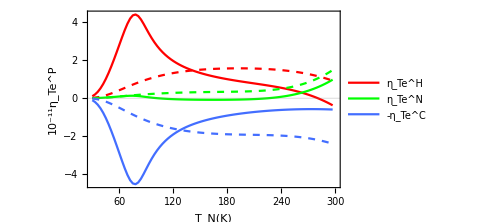

## Plots for adjusting Ω while keeping T_CNT constant (operation as an optically controlled thermal gate)

Temperature of the intermediate bath

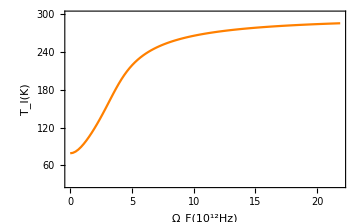

Heat flow comparison between Darlington pair and a single transistor

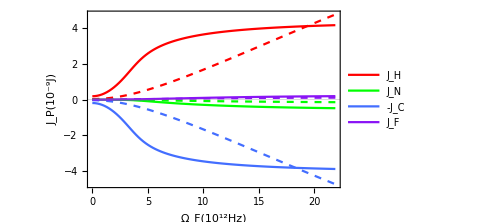
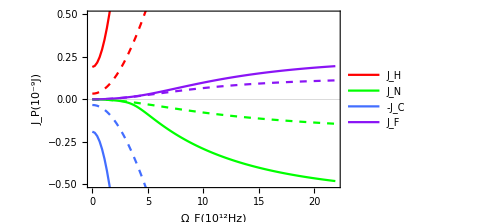

Heat flows of individual transistors

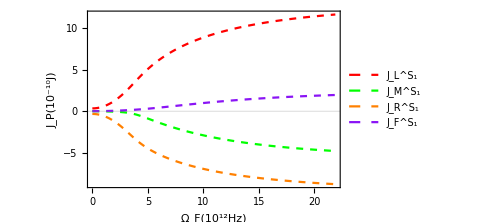

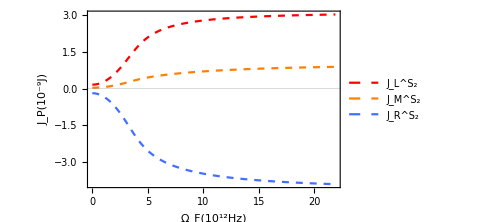

Absolute thermal efficiency

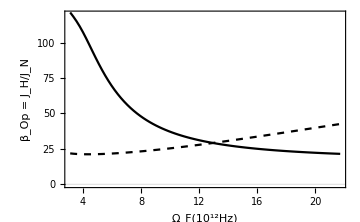

Delta thermal efficiency (amplification factor)

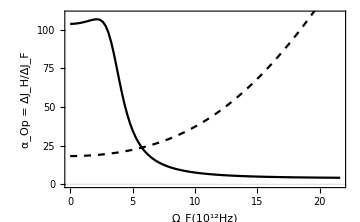

Sensitivity to the optical field

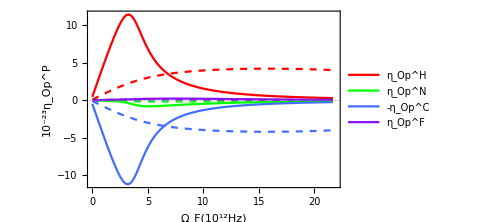

Time domain thermal flows, For m_I C_I=20 mConv

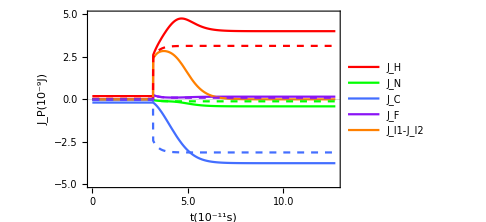

Time domain thermal flows, For m_I C_I=40 mConv